```mathematica
Alnum={132,122,97,77,74};
Alx = {9.60, 19.10, 28.46, 37.90, 47.44};
Alx = Alx * 0.1;
logAlnum = N[Log[Alnum]];
Cunum = {142, 118, 109, 98, 82};
Cux = {2.495, 4.990, 7.485, 9.947, 12.355};
Cux = Cux * 0.1;
logCunum = N[Log[Cunum]];
Pbnum = {133, 115, 96, 78, 68};
Pbx = {1.76, 3.38, 5.24, 7.02, 8.70};
Pbx = Pbx * 0.1;
logPbnum = N[Log[Pbnum]];
Alfit=LinearModelFit[Transpose[{Alx,logAlnum}],x,x];
AlfittedY=Alfit/@Alx;
Alresiduals=logAlnum-AlfittedY;
AlstdY=StandardDeviation[Alresiduals];

Cufit=LinearModelFit[Transpose[{Cux,logCunum}],x,x];
CufittedY=Cufit/@Cux;
Curesiduals=logCunum-CufittedY;
CustdY=StandardDeviation[Curesiduals];


Pbfit=LinearModelFit[Transpose[{Pbx,logPbnum}],x,x];
PbfittedY=Pbfit/@Pbx;
Pbresiduals=logPbnum-PbfittedY;
PbstdY=StandardDeviation[Pbresiduals];



AveXAl = Mean[Alx];
AveXCu =Mean[Cux];
AveXPb=Mean[Pbx];
SmuAl=SmuCu=SmuPb=0;

For[i=1, i<=5, i++, SmuAl = SmuAl+ (Alx[[i]]-AveXAl)^2];
SmuAl = AlstdY/Sqrt[SmuAl ];
For[i=1, i<=5, i++, SmuCu = SmuCu+ (Cux[[i]]-AveXCu)^2];
SmuCu = CustdY/Sqrt[SmuCu ];
For[i=1, i<=5, i++, SmuPb = SmuPb+ (Pbx[[i]]-AveXPb)^2];
SmuPb = PbstdY/Sqrt[SmuPb ];

t =4.3;
UmuAl = t*SmuAl;
UmuCu = t*SmuCu;
UmuPb = t*SmuPb;
Print[UmuAl];
Print[UmuCu];
Print[UmuPb];
```

2.85

27.4788

2.85

8.72988

8.72988

√(6803/10)

8.72988

0.0186576

0.055744

0.0186576

0.0186576

0.0186576

0.0802278

0.0802278

0.125566/(√((0.2495-AveXCu)^2+(0.499-AveXCu)^2+(0.7485-AveXCu)^2+(0.9947-AveXCu)^2+(1.2355-AveXCu)^2))

0.0802278

0.160904

0.0802278

0.160904

0.104414

27.4788

2.85

27.4788

2.85

27.4788

27.4788

√(6803/10)

27.4788

27.4788

27.4788

{0.96,1.91,2.846,3.79,4.744}

27.4788

取自然对数后的数据3: {4.89035,4.74493,4.56435,4.35671,4.21951}

取自然对数后的数据2: {4.95583,4.77068,4.69135,4.58497,4.40672}

取自然对数后的数据1: {4.8828,4.80402,4.57471,4.34381,4.30407}

取自然对数后的数据: {4.89035,4.74493,4.56435,4.35671,4.21951}

取自然对数后的数据: {4.95583,4.77068,4.69135,4.58497,4.40672}

取自然对数后的数据: {4.95583,4.77068,4.69135,4.58497,4.40672}

取自然对数后的数据: {4.8828,4.80402,4.57471,4.34381,4.30407}

取自然对数后的数据: {4.8828,4.80402,4.57471,4.34381,4.30407}

第一组数据拟合结果:

斜率 (slope): -0.0171118

第二组数据拟合结果:

斜率 (slope): -0.0520074

第三组数据拟合结果:

斜率 (slope): -0.0988027

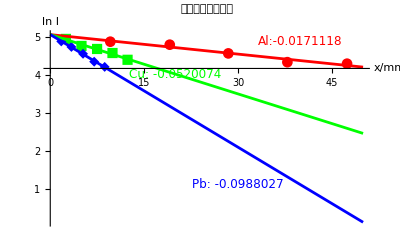

```mathematica
(*将 x 和每组 y 数据组合成二维列表*)
data1=Transpose[{Alx,logAlnum}];
data2=Transpose[{Cux,logCunum}];
data3=Transpose[{Pbx,logPbnum}];

(*使用 Fit 分别进行线性拟合*)
fit1=Fit[data1,{1,x},x]; (*拟合第一组数据*)
fit2=Fit[data2,{1,x},x]; (*拟合第二组数据*)
fit3=Fit[data3,{1,x},x]; (*拟合第三组数据*)

(*提取斜率和截距*)
slope1=Coefficient[fit1,x]; (*第一组斜率*)
slope2=Coefficient[fit2,x]; (*第二组斜率*)
slope3=Coefficient[fit3,x]; (*第三组斜率*)

(*输出拟合结果*)
Print["第一组数据拟合结果:"];
Print["斜率 (slope): ",slope1]

Print["第二组数据拟合结果:"];
Print["斜率 (slope): ",slope2]

Print["第三组数据拟合结果:"];
Print["斜率 (slope): ",slope3]

(*绘制数据点和拟合直线*)
Show[ListPlot[{data1,data2,data3},PlotStyle->{Red,Green,Blue},PlotMarkers->Automatic],(*绘制数据点*)Plot[{fit1,fit2,fit3},{x,0,50},PlotStyle->{Red,Green,Blue}],(*绘制拟合直线*)Graphics[{Text[Style["Al:"<>ToString[slope1],Red,12],{40,fit1/. x->10},{0,-1}],Text[Style["Cu: "<>ToString[slope2],Green,12],{20,fit2/. x->20},{0,-1}],Text[Style["Pb: "<>ToString[slope3],Blue,12],{30,fit3/. x->40},{0,-1}]}],AxesLabel->{"x/mm","ln I"},PlotLabel->"三组数据线性拟合",PlotLegends->{"Al","Cu","Pb"},PlotRange->All
]
```